```mathematica
Remove["Global`*"];
```

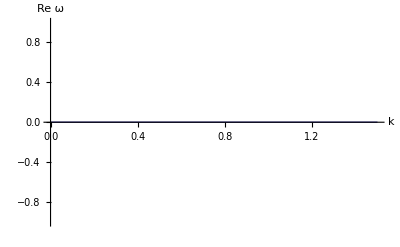

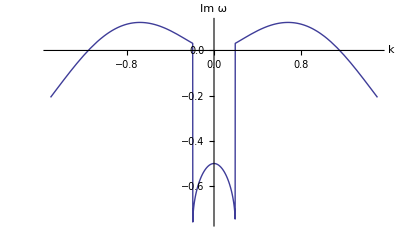

```mathematica
Remove["Global`*"];
L=({{μ(1+k1^2/2), μ, ((ⅈ β γ)/2+(2 γ μ)/(α γR))}, {-μ, -(μ(1+k1^2/2)), ((ⅈ β γ)/2-(2 γ μ)/(α γR))}, {-ⅈ α γR, -ⅈ α γR, -ⅈ(η γR+D1 k1^2 μ)}});
γR=1;
γ=1;
α=0.5;
β=1;
μ=1;
η=1+α β;
D1=0.0005;
feigT=Sort[Eigenvalues[L]];
feig={(*Take[feigT,{1,1}],*)Take[feigT,{2,2}](*,Take[feigT,{3,3}]*)};
Plot[Re[feig],{k1,0,1.5},PlotRange->All,AxesLabel->{"k","Re ω"}]
Plot[Im[feig],{k1,0,1.5},PlotRange->All,AxesLabel->{"k","Im ω"},WorkingPrecision->MachinePrecision]
```